```mathematica
Ukkp[k_, kp_, Ni_, alpha_]:=1/Ni Sum[Exp[I (2 π)/Ni(n+alpha 1/2)(kp+1-k)],{n,0,Ni-1}]
Vkkp[k_, kp_,Ni_, alpha_]:= KroneckerDelta[k, kp] Exp[I (2 π)/Ni(k+alpha 1/2)]
```

```mathematica
U[Ni_, alpha_] := Table[Simplify[Ukkp[i, j, Ni, alpha]],{i,0,Ni-1},{j,0,Ni-1}]
V[Ni_, alpha_] := Table[Simplify[Vkkp[i, j, Ni, alpha]],{i,0,Ni-1},{j,0,Ni-1}]
```

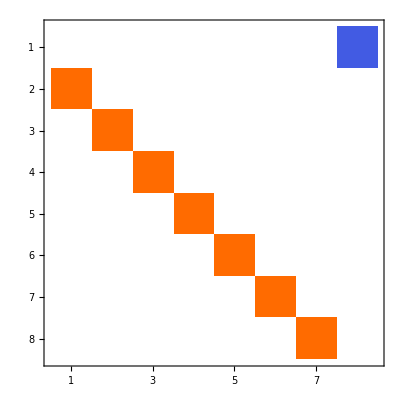

```mathematica
U[8,1]//MatrixPlot
```

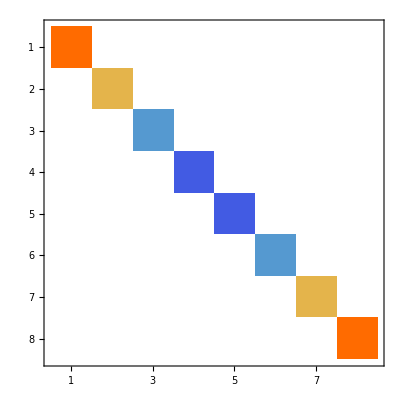

```mathematica
V[8, 1]//MatrixPlot
```

```mathematica
Hermitia
```

```mathematica
H[Ni_, alpha_]:=2 IdentityMatrix[Ni] -(U[Ni, alpha] +U[Ni,alpha]†)/2-(V[Ni, alpha] +V[Ni,alpha]†)/2
```

```mathematica
Eigenvalues[H[8, 1]]
```

{1/2 (4+√(16+Root-5.18Root[{-2+#1^2&,16904-1536 #1+6304 #2-224 #1 #2+840 #2^2-8 #1 #2^2+48 #2^3+#2^4&},{2,4}]-5.18282000230023)),1/2 (4+√(16+Root-11.9Root[{-2+#1^2&,16904-1536 #1+6304 #2-224 #1 #2+840 #2^2-8 #1 #2^2+48 #2^3+#2^4&},{2,3}]-11.900931654051515)),1/2 (4+√(16+Root-15.1Root[{-2+#1^2&,16904-1536 #1+6304 #2-224 #1 #2+840 #2^2-8 #1 #2^2+48 #2^3+#2^4&},{2,2}]-15.121661867654623)),1/2 (4+√(16+Root-15.8Root[{-2+#1^2&,16904-1536 #1+6304 #2-224 #1 #2+840 #2^2-8 #1 #2^2+48 #2^3+#2^4&},{2,1}]-15.794586475993631)),1/2 (4-√(16+Root-15.8Root[{-2+#1^2&,16904-1536 #1+6304 #2-224 #1 #2+840 #2^2-8 #1 #2^2+48 #2^3+#2^4&},{2,1}]-15.794586475993631)),1/2 (4-√(16+Root-15.1Root[{-2+#1^2&,16904-1536 #1+6304 #2-224 #1 #2+840 #2^2-8 #1 #2^2+48 #2^3+#2^4&},{2,2}]-15.121661867654623)),1/2 (4-√(16+Root-11.9Root[{-2+#1^2&,16904-1536 #1+6304 #2-224 #1 #2+840 #2^2-8 #1 #2^2+48 #2^3+#2^4&},{2,3}]-11.900931654051515)),1/2 (4-√(16+Root-5.18Root[{-2+#1^2&,16904-1536 #1+6304 #2-224 #1 #2+840 #2^2-8 #1 #2^2+48 #2^3+#2^4&},{2,4}]-5.18282000230023))}

```mathematica
H1 = H[8,1];
H2 = H[6, 1];
```

```mathematica
Eigenvalues[H1]
```

{1/2 (4+√(16+Root-5.18Root[{-2+#1^2&,16904-1536 #1+6304 #2-224 #1 #2+840 #2^2-8 #1 #2^2+48 #2^3+#2^4&},{2,4}]-5.18282000230023)),1/2 (4+√(16+Root-11.9Root[{-2+#1^2&,16904-1536 #1+6304 #2-224 #1 #2+840 #2^2-8 #1 #2^2+48 #2^3+#2^4&},{2,3}]-11.900931654051515)),1/2 (4+√(16+Root-15.1Root[{-2+#1^2&,16904-1536 #1+6304 #2-224 #1 #2+840 #2^2-8 #1 #2^2+48 #2^3+#2^4&},{2,2}]-15.121661867654623)),1/2 (4+√(16+Root-15.8Root[{-2+#1^2&,16904-1536 #1+6304 #2-224 #1 #2+840 #2^2-8 #1 #2^2+48 #2^3+#2^4&},{2,1}]-15.794586475993631)),1/2 (4-√(16+Root-15.8Root[{-2+#1^2&,16904-1536 #1+6304 #2-224 #1 #2+840 #2^2-8 #1 #2^2+48 #2^3+#2^4&},{2,1}]-15.794586475993631)),1/2 (4-√(16+Root-15.1Root[{-2+#1^2&,16904-1536 #1+6304 #2-224 #1 #2+840 #2^2-8 #1 #2^2+48 #2^3+#2^4&},{2,2}]-15.121661867654623)),1/2 (4-√(16+Root-11.9Root[{-2+#1^2&,16904-1536 #1+6304 #2-224 #1 #2+840 #2^2-8 #1 #2^2+48 #2^3+#2^4&},{2,3}]-11.900931654051515)),1/2 (4-√(16+Root-5.18Root[{-2+#1^2&,16904-1536 #1+6304 #2-224 #1 #2+840 #2^2-8 #1 #2^2+48 #2^3+#2^4&},{2,4}]-5.18282000230023))}

```mathematica
Eigenvalues[H2]
```

{1/4 Root14.2Root[1408-1280 #1+336 #1^2-32 #1^3+#1^4&,4]14.152756005283406,1/4 Root11.2Root[1408-1280 #1+336 #1^2-32 #1^3+#1^4&,3]11.184900868072503,2,2,1/4 Root4.82Root[1408-1280 #1+336 #1^2-32 #1^3+#1^4&,2]4.815099131927497,1/4 Root1.85Root[1408-1280 #1+336 #1^2-32 #1^3+#1^4&,1]1.8472439947165937}

```mathematica
H3 = H[6, 0];
H4 = H[8, 0];
```

```mathematica
Eigenvalues[H3]
```

{1/4 (8+√(64+Root-25.7Root[{-3+#1^2&,1-#2^2+#2^4&,129152-26368 #1 #2+13184 #1 #2^3+7944 #3-944 #1 #2 #3+472 #1 #2^3 #3+156 #3^2-8 #1 #2 #3^2+4 #1 #2^3 #3^2+#3^3&},{2,4,3}]-25.66969722017664)),1/4 (8+√(64+Root-56.0Root[{-3+#1^2&,1-#2^2+#2^4&,129152-26368 #1 #2+13184 #1 #2^3+7944 #3-944 #1 #2 #3+472 #1 #2^3 #3+156 #3^2-8 #1 #2 #3^2+4 #1 #2^3 #3^2+#3^3&},{2,4,2}]-56.)),1/4 (8+√(64+Root-62.3Root[{-3+#1^2&,1-#2^2+#2^4&,129152-26368 #1 #2+13184 #1 #2^3+7944 #3-944 #1 #2 #3+472 #1 #2^3 #3+156 #3^2-8 #1 #2 #3^2+4 #1 #2^3 #3^2+#3^3&},{2,4,1}]-62.33030277982336)),1/4 (8-√(64+Root-62.3Root[{-3+#1^2&,1-#2^2+#2^4&,129152-26368 #1 #2+13184 #1 #2^3+7944 #3-944 #1 #2 #3+472 #1 #2^3 #3+156 #3^2-8 #1 #2 #3^2+4 #1 #2^3 #3^2+#3^3&},{2,4,1}]-62.33030277982336)),1/4 (8-√(64+Root-56.0Root[{-3+#1^2&,1-#2^2+#2^4&,129152-26368 #1 #2+13184 #1 #2^3+7944 #3-944 #1 #2 #3+472 #1 #2^3 #3+156 #3^2-8 #1 #2 #3^2+4 #1 #2^3 #3^2+#3^3&},{2,4,2}]-56.)),1/4 (8-√(64+Root-25.7Root[{-3+#1^2&,1-#2^2+#2^4&,129152-26368 #1 #2+13184 #1 #2^3+7944 #3-944 #1 #2 #3+472 #1 #2^3 #3+156 #3^2-8 #1 #2 #3^2+4 #1 #2^3 #3^2+#3^3&},{2,4,3}]-25.66969722017664))}

```mathematica
Eigenvalues[H4]
```

{(1/4+ⅈ/4) Root7.29-7.29 ⅈRoot[{-2+#1^2&,1+#2^4&,1+#3^2&,413440-12288 #1+8352 #2-53664 #1 #2+12288 #2^3+17888 #1 #2^3+53664 #1 #2 #3+20640 #2^3 #3+17888 #1 #2^3 #3-537600 #4+7168 #1 #4+56896 #2 #4+95056 #1 #2 #4-20528 #2^3 #4+«63»+290 #2^3 #4^5-16 #1 #2^3 #4^5+6592 #3 #4^5-290 #2 #3 #4^5+16 #1 #2 #3 #4^5-890 #2^3 #3 #4^5+16 #1 #2^3 #3 #4^5+4 #1 #2 #4^6+2 #1 #2^3 #4^6-872 #3 #4^6+2 #1 #2 #3 #4^6-32 #4^7+32 #3 #4^7+#4^8&},{2,4,2,8}]7.290657552032145,(1/4+ⅈ/4) Root6.00-6.00 ⅈRoot[{-2+#1^2&,1+#2^4&,1+#3^2&,413440-12288 #1+8352 #2-53664 #1 #2+12288 #2^3+17888 #1 #2^3+53664 #1 #2 #3+20640 #2^3 #3+17888 #1 #2^3 #3-537600 #4+7168 #1 #4+56896 #2 #4+95056 #1 #2 #4-20528 #2^3 #4+«63»+290 #2^3 #4^5-16 #1 #2^3 #4^5+6592 #3 #4^5-290 #2 #3 #4^5+16 #1 #2 #3 #4^5-890 #2^3 #3 #4^5+16 #1 #2^3 #3 #4^5+4 #1 #2 #4^6+2 #1 #2^3 #4^6-872 #3 #4^6+2 #1 #2 #3 #4^6-32 #4^7+32 #3 #4^7+#4^8&},{2,4,2,7}]6.,(1/4+ⅈ/4) Root5.08-5.08 ⅈRoot[{-2+#1^2&,1+#2^4&,1+#3^2&,413440-12288 #1+8352 #2-53664 #1 #2+12288 #2^3+17888 #1 #2^3+53664 #1 #2 #3+20640 #2^3 #3+17888 #1 #2^3 #3-537600 #4+7168 #1 #4+56896 #2 #4+95056 #1 #2 #4-20528 #2^3 #4+«63»+290 #2^3 #4^5-16 #1 #2^3 #4^5+6592 #3 #4^5-290 #2 #3 #4^5+16 #1 #2 #3 #4^5-890 #2^3 #3 #4^5+16 #1 #2^3 #3 #4^5+4 #1 #2 #4^6+2 #1 #2^3 #4^6-872 #3 #4^6+2 #1 #2 #3 #4^6-32 #4^7+32 #3 #4^7+#4^8&},{2,4,2,6}]5.082392200292394,(1/4+ⅈ/4) Root4.00-4.00 ⅈRoot[{-2+#1^2&,1+#2^4&,1+#3^2&,413440-12288 #1+8352 #2-53664 #1 #2+12288 #2^3+17888 #1 #2^3+53664 #1 #2 #3+20640 #2^3 #3+17888 #1 #2^3 #3-537600 #4+7168 #1 #4+56896 #2 #4+95056 #1 #2 #4-20528 #2^3 #4+«63»+290 #2^3 #4^5-16 #1 #2^3 #4^5+6592 #3 #4^5-290 #2 #3 #4^5+16 #1 #2 #3 #4^5-890 #2^3 #3 #4^5+16 #1 #2^3 #3 #4^5+4 #1 #2 #4^6+2 #1 #2^3 #4^6-872 #3 #4^6+2 #1 #2 #3 #4^6-32 #4^7+32 #3 #4^7+#4^8&},{2,4,2,5}]4.,(1/4+ⅈ/4) Root4.00-4.00 ⅈRoot[{-2+#1^2&,1+#2^4&,1+#3^2&,413440-12288 #1+8352 #2-53664 #1 #2+12288 #2^3+17888 #1 #2^3+53664 #1 #2 #3+20640 #2^3 #3+17888 #1 #2^3 #3-537600 #4+7168 #1 #4+56896 #2 #4+95056 #1 #2 #4-20528 #2^3 #4+«63»+290 #2^3 #4^5-16 #1 #2^3 #4^5+6592 #3 #4^5-290 #2 #3 #4^5+16 #1 #2 #3 #4^5-890 #2^3 #3 #4^5+16 #1 #2^3 #3 #4^5+4 #1 #2 #4^6+2 #1 #2^3 #4^6-872 #3 #4^6+2 #1 #2 #3 #4^6-32 #4^7+32 #3 #4^7+#4^8&},{2,4,2,5}]4.,(1/4+ⅈ/4) Root2.92-2.92 ⅈRoot[{-2+#1^2&,1+#2^4&,1+#3^2&,413440-12288 #1+8352 #2-53664 #1 #2+12288 #2^3+17888 #1 #2^3+53664 #1 #2 #3+20640 #2^3 #3+17888 #1 #2^3 #3-537600 #4+7168 #1 #4+56896 #2 #4+95056 #1 #2 #4-20528 #2^3 #4+«63»+290 #2^3 #4^5-16 #1 #2^3 #4^5+6592 #3 #4^5-290 #2 #3 #4^5+16 #1 #2 #3 #4^5-890 #2^3 #3 #4^5+16 #1 #2^3 #3 #4^5+4 #1 #2 #4^6+2 #1 #2^3 #4^6-872 #3 #4^6+2 #1 #2 #3 #4^6-32 #4^7+32 #3 #4^7+#4^8&},{2,4,2,3}]2.917607799707606,(1/4+ⅈ/4) Root2.00-2.00 ⅈRoot[{-2+#1^2&,1+#2^4&,1+#3^2&,413440-12288 #1+8352 #2-53664 #1 #2+12288 #2^3+17888 #1 #2^3+53664 #1 #2 #3+20640 #2^3 #3+17888 #1 #2^3 #3-537600 #4+7168 #1 #4+56896 #2 #4+95056 #1 #2 #4-20528 #2^3 #4+«63»+290 #2^3 #4^5-16 #1 #2^3 #4^5+6592 #3 #4^5-290 #2 #3 #4^5+16 #1 #2 #3 #4^5-890 #2^3 #3 #4^5+16 #1 #2^3 #3 #4^5+4 #1 #2 #4^6+2 #1 #2^3 #4^6-872 #3 #4^6+2 #1 #2 #3 #4^6-32 #4^7+32 #3 #4^7+#4^8&},{2,4,2,2}]2.,(1/4+ⅈ/4) Root0.709-0.709 ⅈRoot[{-2+#1^2&,1+#2^4&,1+#3^2&,413440-12288 #1+8352 #2-53664 #1 #2+12288 #2^3+17888 #1 #2^3+53664 #1 #2 #3+20640 #2^3 #3+17888 #1 #2^3 #3-537600 #4+7168 #1 #4+56896 #2 #4+95056 #1 #2 #4-20528 #2^3 #4+«63»+290 #2^3 #4^5-16 #1 #2^3 #4^5+6592 #3 #4^5-290 #2 #3 #4^5+16 #1 #2 #3 #4^5-890 #2^3 #3 #4^5+16 #1 #2^3 #3 #4^5+4 #1 #2 #4^6+2 #1 #2^3 #4^6-872 #3 #4^6+2 #1 #2 #3 #4^6-32 #4^7+32 #3 #4^7+#4^8&},{2,4,2,1}]0.7093424479678548}

```mathematica
Ukkp[1, 0, 8]
```

1

```mathematica
Table[Simplify[Ukkp[i, j, 8]],{i,0,7},{j,0,7}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)